# GMRES Generalized Minimum Residual

We are going to iteratively approximate the solution of 
	A.x=b
using the Krylov space
	𝒦_n(A,b):=span({b,A.b,A^2.b,…,A^(n-1).b}).
The polynomial 
	q(A)=c_0 Id+c_1 A+ c_2 A^2+…+c_(n-1)A^(n-1) 
(remember x∈𝒦_n(A,b)  satisfies x=c_0 b+c_1 A.b+ c_2 A^2.b+…+c_(n-1)A^(n-1).b=q(A).b) is going to make another appearance and the target x_exact=A^-1.b satisfies A.x_exact=b.

## Arnoldi Reminder

Just as a reminder: The Arnoldi process iteratively computes a nested sequence of orthogonal matrices Q_n∈ℝ^(m×n) and rectangular Upper Hessenberg matrices H_n∈ℝ^((n+1)×n).  Columns of Q_n are an orthonormal basis for the Krylov space	
	𝒦_n(A,b):=span({b,A.b,A^2.b,…,A^(n-1).b}).
By construction, A maps 𝒦_n(A,b)→𝒦_(n+1)(A,b) with H_n the matrix for this map in the orthogonal basis. In other words, since H_n is Upper Hessenberg
	A.Q_n=Q_(n+1).H_n=Q_n.H_n[1:n,1:n]+H_n[n+1,n] q_(n+1). 
If the bottom corner of H_n is zero the Q_n is an invariant space of A.

```mathematica
Arnoldi[A_][{Q_,H_}]:= Module[{m,n,HNew,w,h,q},
{m,n}=Dimensions[Q];
HNew=ConstantArray[0,{n+1,n}];HNew⟦1;;n,1;;n-1⟧=H;
w=A.Q⟦All,n⟧;
Do[
q=Q⟦All,k⟧;
HNew⟦k,n⟧=q.w;
w=w-HNew⟦k,n⟧ q,
{k,1,n}];
HNew⟦n+1,n⟧=Norm[w];
w=w/HNew⟦n+1,n⟧;
{ArrayFlatten[({{Q, {w}ᵀ}})],HNew}
]
```

Remember:

Q_n is an orthogonal basis for the something approximating the “large” eigenspace of A

Q_(n+1)=[Q_n|q_(n+1)]

By construction multiplying by A maps 𝒦_n→𝒦_(n+1) and the map is expressed by H_n

H_n=((Ĥ)_n
0,…,0,H_(n+1,n)) is a rectangular Hessenberg matrix.

## GMRES

The GMRES approximation is simply
	x_n=argmin_(x∈𝒦_n)||A.x-b||
The name is simply a mnemonic for Generalized Minimum Residual.

We have a convenient basis for 𝒦_n so we write x_n=Q_n.y_n and note that
	y_n=argmin_(y∈ℝ^n)||A.Q_n.y-b||=argmin_y||Q_(n+1).H_n.y-b||
In words, y_n is the best solution in 𝒦_n and the Arnoldi construction lets us explicitly flip things into the one larger space. We are nearly done remember b∈𝒦_(n+1) and (Q_(n+1))ᵀ.b=e_1 and Q_(n+1) is orthogonal so
		y_n=argmin_y||Q_(n+1).H_n.y-b||=argmin_y||H_n.y-(Q_(n+1))ᵀ.b||=argmin_y||H_n.y-||b||e_1||
The last problem is a small linear least squares problem with an almost triangular right hand side.

Since we already have Arnoldi code this will be pretty easy to code.

The question is how fast does it converge?

The residuals r_n=b-A.x_n satisfy
	||r_n||=min_(x∈𝒦_n) ||A.x-b||=min_(y∈ℝ^n) ||H_n.y-||b||e_1||

||r_(n+1)||≤||r_n|| since 𝒦_(n+1)⊃𝒦_n.

The residuals are given by polynomials in A i.e.
	x_n=(c_1 A^0+c_2 A^1+…+c_n A^(n-1)).b

r_n=b-A.x_n=(I_m-A.(c_1 A^0+c_2 A^1+…+c_n A^(n-1))).b

By definition, GMRES produces best optimal polynomial in the space 𝒫_n^GMRES={1+a_1 z+…+a_n z^n}.

p_n^GMRES=argmin_(p∈𝒫_n^GMRES)|| p(A).b||

Since we run out of dimensions when n=m we know that r_m=0.

The induced matrix norm satisfies ||p(A).b||≤||p(A)(||)_induced||b|| for any polynomial. So we have

(||r_n||)/(||b||)=(||p_n^GMRES(A).b||)/(||b||)≤(||p(A).b||)/(||b||)≤||p(A)(||)_induced  for any p∈𝒫_n^GMRES

If A lets us pick polynomials p∈𝒫_n^GMRES with p(A) small then we know the residuals get small fast.

We are going to come back to this once we see the GMRES in action.

## GMRES in Action.

Here is a special matrix with a plot of its spectrum.

```mathematica
m=123;
ϵ=3.0;
Dia=DiagonalMatrix[Range[1,m]];
ARand=RandomReal[{-1,1},{m,m}];
A=ϵ ARand + Dia;
TabView[{
"Mat"->MatrixPlot[A],
"Evals"->ListPlot[ReIm[Eigenvalues[A]]]
}]
```

12

As you might expect some eigenvalues are all sorts close to the large diagonal entries! The spectrum is all spread out! Lets see how GMRES does on this matrix.

```mathematica
b=RandomReal[{-1,1},m];
xMma=LinearSolve[A,b];
MaxIter=40;
bNorm=Norm[b];
{Q,H}={{b/bNorm}ᵀ,{{}}};
xData=Table[
{Q,H}=Arnoldi[A][{Q,H}];
y=LeastSquares[H,SparseArray[1->bNorm,Length[H]]];
x=Q⟦All,1;;-2⟧.y,
{MaxIter}];
dData=Map[Norm[#-xMma]&,xData];
rData=Map[Norm[A.#-b]&,xData];
TabView[{
"rData"->ListLogPlot[rData,Frame->True],
"xData"->MatrixPlot[xData],
"dData"->ListLogPlot[dData,Frame->True],
"r&dData"->ListLogPlot[{rData,dData},Frame->True,
PlotLegends->{"r","d"}]}]
```

1234

It is converging! It is not converging fast! A very simple trick will fix this problem. Instead of solving 
	(ϵ ARand+Dia).x=b
we are going to solve the completely equivalent system
	Dia^-1.(ϵ ARand+Dia).x=Dia^-1.b
using GMRES. Take a look at the spectra. See if you can see what makes the second one better!

```mathematica
A=ϵ ARand+Dia;
TabView[{
"Λ(A)"->ListPlot[ReIm[Eigenvalues[ϵ ARand+Dia]],PlotRange->All,
Prolog->{LightGreen,EdgeForm[Red],Disk[{1,0},1]},
AspectRatio->Automatic],
"Λ(Dia^-1.A)"->ListPlot[ReIm[Eigenvalues[Inverse[Dia].A]],PlotRange->All,Prolog->{LightGreen,EdgeForm[Red],Disk[{1,0},1]},
AspectRatio->Automatic]
}]
```

12

```mathematica
b=RandomReal[{-1,1},m];
xMma=LinearSolve[A,b];
MaxIter=40;
DInvA=Inverse[Dia].A;
DInvb=Inverse[Dia].b;
DInvbNorm=Norm[DInvb];
{Q,H}={{DInvb/DInvbNorm}ᵀ,{{}}};
xData=Table[
{Q,H}=Arnoldi[DInvA][{Q,H}];
y=LeastSquares[H,SparseArray[1->DInvbNorm,Length[H]]];
x=Q⟦All,1;;-2⟧.y,
{MaxIter}];
dData=Map[Norm[#-xMma]&,xData];
rData=Map[Norm[DInvA.#-DInvb]&,xData];
TabView[{
"rData"->ListLogPlot[rData,Frame->True],
"xData"->MatrixPlot[xData],
"dData"->ListLogPlot[dData,Frame->True],
"r&dData"->ListLogPlot[{rData,dData},Frame->True,
PlotLegends->{"r","d"}]}]
```

1234

It is converging much faster!  We could estimate the convergence by looking at the spectrum. The GMRES residual r_n goes to zero faster than any “any nth degree polynomial of the form 1+c_1 z+… on the spectrum”.  It is easy to make a polynomial which is small on a clustered spectrum!

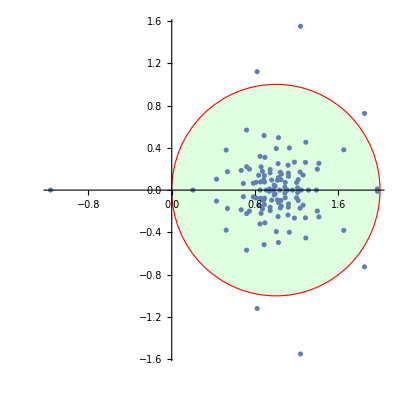

```mathematica
ListPlot[ReIm[Eigenvalues[Inverse[Dia].A]],PlotRange->All,Prolog->{LightGreen,EdgeForm[Red],Disk[{1,0},1]},
AspectRatio->Automatic]
```

The standard way to “cluster” a spectrum is to try to generate a cheap approximate inverse since
	M≈A^-1
ought to mean 
	M.A≈A^-1.A=I
which has a very clustered spectrum Λ(I)={1}. If the 
	Λ(M.A)⊂B_d(1)
with radius d<1 then spectrum the polynomial (1-z)^n satisfies 
	Abs[(1-z)^n]≤d^n
and we have at least geometric convergence with rate d!

The approximate inverse M≈A^-1 is called a preconditioner for A. In practice preconditioners are necessary to make iterative schemes efficient!

## ILU Preconditioners

ILU preconditioners improve convergence greatly for numerous physical systems.  The idea is pretty simple.  The basic idea is to limit the fill-in that happens for a sparse matrix when you perform an LU decomposition! The simplest fill limiters are: only compute entries in M with non-zero entries in A and/or do not compute entries less than some relative tolerance τ.

The simplest of all preconditioners is the diagonal matrix we used above: this is dressed up by calling it the Jacobi preconditioner! Mathematica has an ILU preconditioner to implement its iterative solvers. It is NOT documented.

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/SPARSKIT/drivcav/e20r0100.mtx.gz"];
m=Length[A]; Id=SparseArray[Band[{1,1}]->1.0,{m,m}];
A=A+Id
{LU,piv,cond}=LUDecomposition[A];
{ILU,Spiv}=SparseArray`SparseMatrixILU[A];
{IL,IU}={LowerTriangularize[ILU,-1]+Id, U=UpperTriangularize[ILU]}
TabView[{
"A"->MatrixPlot[A],
"LU"->MatrixPlot[LU],
"IL"->MatrixPlot[IL],
"IU"->MatrixPlot[IU]}]
```

SparseArray[<132629>, {4241, 4241}]

{SparseArray[<131896>, {4241, 4241}],SparseArray[<135028>, {4241, 4241}]}

1234

A real question is how good is the ILU. There are several ways to answer this.

```mathematica
ILIU=IL.IU;
InvILIU=Inverse[Normal[ILIU]];
InvILIUA=InvILIU.A;
{Norm[A-ILIU,"Frobenius"]/Norm[A,"Frobenius"],Norm[InvILIUA-Id,"Frobenius"]/Norm[A,"Frobenius"]}
```

{0.002091,0.000527171}

The best thing to do is look at the spectra.

```mathematica
TabView[{
"Λ(A)"->ListPlot[ReIm[Eigenvalues[Normal[A]]],PlotRange->All],
"Λ(M.A)"->ListPlot[ReIm[Eigenvalues[InvILIUA]],PlotRange->All]
}]
```

12

We should expect preconditioned GMRES to converge with a rate something like 0.006^n which is pretty good! We would expect GMRES to resolve to machine precision in about 8 steps since 	
	0.006^8≈1.67962×10^-18.